## Define inner product here

```mathematica
ip[u_,v_]:= Integrate[u v,{x,0,X}]
```

## Define vectors here

```mathematica
u = {x^2-X^2,x^2(x-X),x^2 (x-X)^3}
```

{x^2-X^2,x^2 (x-X),x^2 (x-X)^3}

Print out the vectors in LaTeX

```mathematica
TeXForm[u]
```

\left\{x^2-X^2,x^2 (x-X),x^2 (x-X)^3\right\}

## Compute Values

Define a table to hold the orthogonal vectors

```mathematica
v=Table[i,{i,1,Length[u]}]
```

{1,2,3}

Loop over vectors, applying GS formula

```mathematica
For[i=1,i≤ Length[u],i++,

v[[i]] =FullSimplify[ u[[i]] - Sum[ip[u[[i]],v[[j]]]/ip[v[[j]],v[[j]]] * v[[j]],{j,1,i-1}]];
v[[i]] = FullSimplify[v[[i]]/Sqrt[ip[v[[i]],v[[i]]]]]]
```

Print out the orthogonal vectors

```mathematica
v
```

{(√(15/2) (x-X) (x+X))/(2 √(X^5)),(√(21/26) (32 x^3-35 x^2 X+3 X^3))/(2 √(X^7)),(√(33/20813) (2730 x^5-8190 x^4 X+7987 x^3 X^2-2575 x^2 X^3+48 X^5))/(√(X^11))}

```mathematica
Integrate[v[[2]] v[[2]],{x,0,X}]
```

1

```mathematica
TeXForm[v]
```

\left\{\frac{\sqrt{\frac{15}{2}} (x-X) (x+X)}{2 \sqrt{X^5}},\frac{\sqrt{\frac{21}{26}}
   \left(32 x^3-35 x^2 X+3 X^3\right)}{2 \sqrt{X^7}},\frac{\sqrt{\frac{33}{20813}}
   \left(2730 x^5-8190 x^4 X+7987 x^3 X^2-2575 x^2 X^3+48
   X^5\right)}{\sqrt{X^{11}}}\right\}

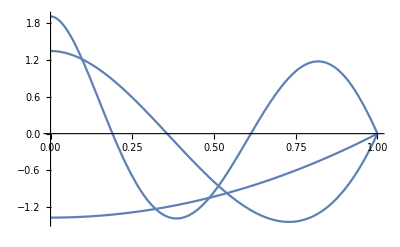

```mathematica
Plot[v/.X->1,{x,0,1},PlotRange->All]
```

Check BC at x = X

```mathematica
v/.{x->X}
```

{0,0,0}

Check BC at x=0

```mathematica
ReleaseHold[Hold[D[v,x]/.x-> 0]]
```

{0,0,0}